{3,1.75,2.15,1,5,12,1000}

{40,0.05,2}

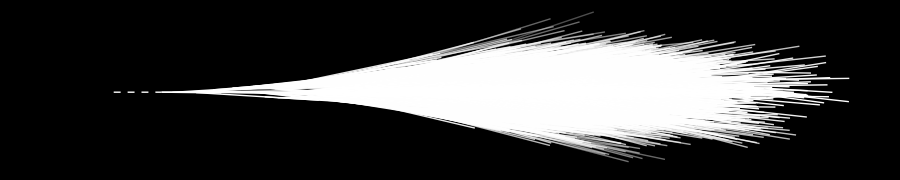

```mathematica
SeedRandom[3]
op={x,y};
p={op,ang,leng,gen};
PL={};(*particle list*)
OP[x_]:=PL⟦x,1⟧
ANG[x_]:=PL⟦x,2⟧
LEN[x_]:=PL⟦x,3⟧
GEN[x_]:=PL⟦x,4⟧
{angspread,minlen,maxlen,minnchi,maxnchi,genlimit,npart}={3,1.75,2.15,1,5,12,1000}

{a1,b1,c1}={40,0.05,2}
FF[x_]:=Sqrt[c1 b1-(x^2 b1)/a1]
InBound[f_]:=Module[{},
{fx,fy}=f;
If[Abs[fy]<FF[fx],
True,False]
]

GenChildren[tid_]:=Module[{j,nchild,op,ang,len,cop,cang,clen,gen,cgen},
If[tid<8,
nchild=2,
nchild=Random[Integer,{minnchi,maxnchi}]
];
op=OP[tid];
ang=ANG[tid];
len=LEN[tid];
gen=GEN[tid];
If[InBound[op],
For[j=0,j<nchild,j++,
cop=op+(RandomReal[]*len*{Cos[ang],Sin[ang]});
cang=ang+Random[Integer,{-angspread,angspread}]°;
clen=(maxlen-minlen)*RandomReal[]+minlen;
cgen=gen+1;
AppendTo[PL,{cop,cang,clen,cgen}]
]
]
]

pinit={{0,0},0.5°,1,1};
AppendTo[PL,pinit];
pinit={{0,0},-0.5°,1,1};
AppendTo[PL,pinit];

For[i=1,i≤npart,i++,
If[GEN[i]>genlimit,Print["Stopped due to GenLimit"];i=npart+20;Break];
GenChildren[i];
]
PL//TableForm;

GFXL={};
Clear[i];
For[i=1,i≤Length[PL],i++,
op=OP[i];
ang=ANG[i];
len=LEN[i];
{opx,opy}=op;
{op2x,op2y}=op+len*{Cos[ang],Sin[ang]};
op2={op2x,op2y};
line=If[i<3,
{White,Thin,Opacity[1-(opy*op2y*1.5)],Line[{op,op2}]},
{White,Thin,Opacity[1-(opy*op2y*1.5)],Line[{op,op2}]}
];
AppendTo[GFXL,line]
];
AppendTo[GFXL,{White,Dashed,Thick,Line[{{-0.8,0},{0,0}}]}];
pl=Plot[{FF[x],-FF[x]},{x,0,20},PlotRange->{-5,5},PlotStyle->{White,White}];
Showergfx=Show[Graphics[GFXL],PlotRange->All,AspectRatio->0.2,Frame->True,FrameStyle->White,Background->Black]
```

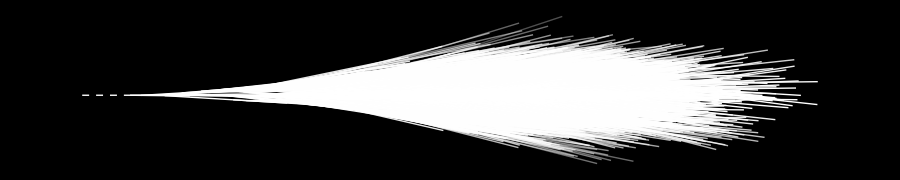

```mathematica
Showergfx=Show[Graphics[GFXL],PlotRange->All,AspectRatio->0.2,ImageSize->900,Background->Black]
```

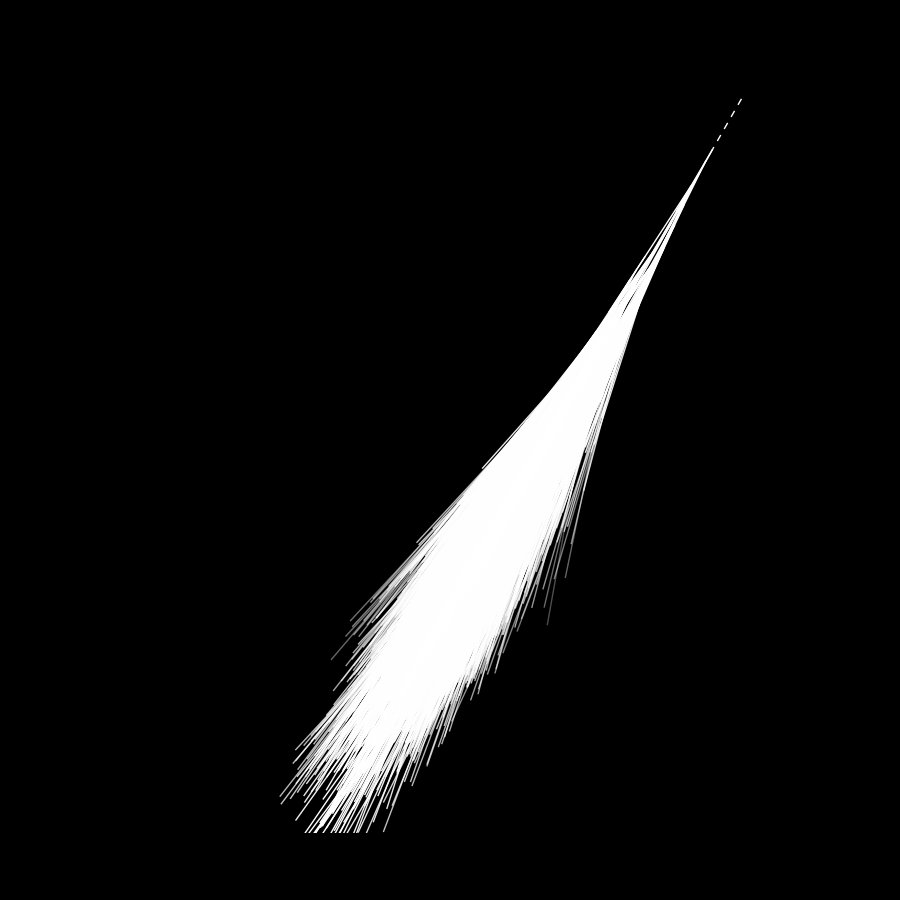

```mathematica
Showerfx[{x_,y_},ang_]:=Show[Graphics[Rotate[Translate[GFXL,{x,y}],ang,{x,y}]],PlotRange->All,AspectRatio->0.4,ImageSize->900,Background->Black]
Show[Showerfx[{0,10},-110°],PlotRange->{{-6,1},{0,11}},AspectRatio->1]
```

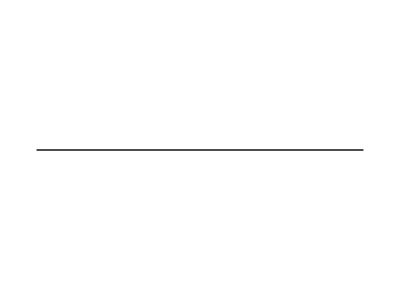

```mathematica
gnd={Black,Line[{{0,0},{6,0}}]};
tank={,};
Show[Graphics[{gnd}],PlotRange->All]
```

## Life of a Gamma Ray

{0.25,0.8}

{0.7,1/2}

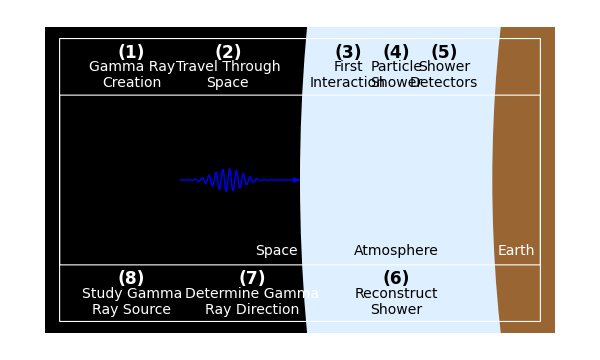

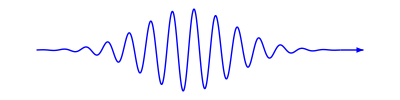

RowBox[{"Export", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"file\",\"TI\"]\).\!\(\*StyleBox[\"ext\",\"TI\"]\)\"",ShowStringCharacters->True], ",", StyleBox["expr", "TI"]}], "]"}] exports data to a file, converting it to the format corresponding to the file extension StyleBox["ext", "TI"]. 
RowBox[{"Export", "[", RowBox[{StyleBox["file", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["\"\!\(\*StyleBox[\"format\",\"TI\"]\)\"", ShowStringCharacters->True]}], "]"}] exports data in the specified format.
RowBox[{"Export", "[", RowBox[{StyleBox["file", "TI"], ",", StyleBox["exprs", "TI"], ",", StyleBox["elems", "TI"]}], "]"}] exports data by treating StyleBox["exprs", "TI"] as elements specified by StyleBox["elems", "TI"].

```mathematica
{x,y,w,h}={2,1,0.3,0.02};
{tx1h,tx2h}={(y/2)-w+0.05,(y/2)+w}
Bkg=Graphics[{
Black,
Rectangle[{-x,-y},{2x,2y}]
}];
Planet=Graphics[{
fntsz=14;
{LightBlue,Disk[{6,y/2},5]},
{Brown,Disk[{6,y/2},4.2]},
{White,
Text[Style["Space",fntsz],{x/2-0.1,tx1h}],
Text[Style["Earth",fntsz],{(3x/4)+0.4,tx1h}]},
{Black,Text[Style["Atmosphere",fntsz],{1.4,tx1h}]}
}];
Wli=Graphics[{
FaceForm[Opacity[0]],EdgeForm[White],
Rectangle[{0,0},{x,y}],
Rectangle[{0,(y/2)-w},{x,(y/2)+w}]
}];
BigText[coord_,ta_,tb_,tc_]:={
Text[Style[ta,17,tc,Bold],coord+{0,0.04}],
Text[Style[tb,14,tc],coord+{0,-0.04}]
}
txtlist=Graphics[{
{tyh1,tyh2}={(y/2)+w+0.11,(y/2)-w-0.09};
BigText[{0.3,tyh1},"(1)","Gamma Ray\nCreation",White],
BigText[{0.7,tyh1},"(2)","Travel Through\nSpace",White],
BigText[{1.2,tyh1},"(3)","First\nInteraction",Black],
BigText[{1.4,tyh1},"(4)","Particle\nShower",Black],
BigText[{1.6,tyh1},"(5)","Shower\nDetectors",Black],
BigText[{1.4,tyh2},"(6)","Reconstruct\nShower",Black],
BigText[{0.8,tyh2},"(7)","Determine Gamma\nRay Direction",White],
BigText[{0.3,tyh2},"(8)","Study Gamma\nRay Source",White]
}];
{x2,y2}={0.7,y/2}
GRay=Plot[y2+0.04*Sin[220*(x1-x2)]*Exp[-(x1-x2)^2/0.007],{x1,x2-0.2,x2+0.2},
PlotRange->All,PlotStyle->Directive[Thick,Blue]];
Show[
Bkg,
Planet,
Wli,
txtlist,
Graphics[{Blue,Thick,Arrow[{{0.9,y/2},{1.0,y/2}}]}],
GRay,
PlotRange->{{-h,x+h},{-h,y+h}},AspectRatio->0.6,ImageSize->600]
```